# Fuzzy measurements and PCEs

## Density matrix for a 2-qubit system

```mathematica
α[0,0]=1;GenericTwoQubitRho=Table[α[i,j],{i,0,3},{j,0,3}]
```

{{1,α[0,1],α[0,2],α[0,3]},{α[1,0],α[1,1],α[1,2],α[1,3]},{α[2,0],α[2,1],α[2,2],α[2,3]},{α[3,0],α[3,1],α[3,2],α[3,3]}}

```mathematica
GenericTwoQubitRho//MatrixForm
```

(1 | α[0,1] | α[0,2] | α[0,3]
α[1,0] | α[1,1] | α[1,2] | α[1,3]
α[2,0] | α[2,1] | α[2,2] | α[2,3]
α[3,0] | α[3,1] | α[3,2] | α[3,3])

```mathematica
GenericTwoQubitRho*TwoQubitPCEGs[[8]]//MatrixForm
```

(1 | 0 | 0 | α[0,3]
α[1,0] | 0 | 0 | α[1,3]
0 | α[2,1] | α[2,2] | 0
0 | α[3,1] | α[3,2] | 0)

```mathematica
Transpose[GenericTwoQubitRho*TwoQubitPCEGs[[8]]]//MatrixForm
```

(1 | α[1,0] | 0 | 0
0 | 0 | α[2,1] | α[3,1]
0 | 0 | α[2,2] | α[3,2]
α[0,3] | α[1,3] | 0 | 0)

```mathematica
Transpose[GenericTwoQubitRho]*TwoQubitPCEGs[[8]]//MatrixForm
```

(1 | 0 | 0 | α[3,0]
α[0,1] | 0 | 0 | α[3,1]
0 | α[1,2] | α[2,2] | 0
0 | α[1,3] | α[2,3] | 0)

```mathematica
#+Transpose[#]&[TwoQubitPCEGs[[8]]]//MatrixForm
```

(2 | 1 | 0 | 1
1 | 0 | 1 | 2
0 | 1 | 2 | 1
1 | 2 | 1 | 0)

Cuando sólo tenemos Fuzzy measurements:

```mathematica
Transpose[GenericTwoQubitRho]//MatrixForm
```

(1 | α[1,0] | α[2,0] | α[3,0]
α[0,1] | α[1,1] | α[2,1] | α[3,1]
α[0,2] | α[1,2] | α[2,2] | α[3,2]
α[0,3] | α[1,3] | α[2,3] | α[3,3])

Cuando sólo tenemos decoherencia (“procesos PCEs”):

```mathematica
TwoQubitPCEGs[[8]]*GenericTwoQubitRho//MatrixForm
```

(1 | 0 | 0 | α[0,3]
α[1,0] | 0 | 0 | α[1,3]
0 | α[2,1] | α[2,2] | 0
0 | α[3,1] | α[3,2] | 0)

```mathematica
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};a//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1)

```mathematica
TwoQubitPCEGs=ArrayReshape[ReplaceAll[KroneckerProduct[a,a],-1->0],{16,4,4}]
```

{{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{1,0,1,0},{1,0,1,0},{1,0,1,0},{1,0,1,0}},{{1,0,0,1},{1,0,0,1},{1,0,0,1},{1,0,0,1}},{{1,1,1,1},{1,1,1,1},{0,0,0,0},{0,0,0,0}},{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{{1,0,1,0},{1,0,1,0},{0,1,0,1},{0,1,0,1}},{{1,0,0,1},{1,0,0,1},{0,1,1,0},{0,1,1,0}},{{1,1,1,1},{0,0,0,0},{1,1,1,1},{0,0,0,0}},{{1,1,0,0},{0,0,1,1},{1,1,0,0},{0,0,1,1}},{{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{1,1,1,1},{0,0,0,0},{0,0,0,0},{1,1,1,1}},{{1,1,0,0},{0,0,1,1},{0,0,1,1},{1,1,0,0}},{{1,0,1,0},{0,1,0,1},{0,1,0,1},{1,0,1,0}},{{1,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,0,1}}}

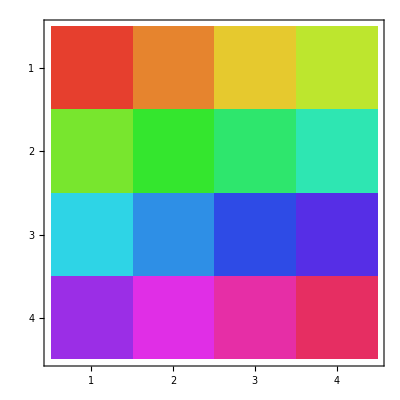

```mathematica
MatrixPlot[ArrayReshape[Range[16],{4,4}],ColorRules->Table[(h*n-1)/4+1->Hue[h,.8,.9],{h,1/n,1-2/n,4/n}]]
```

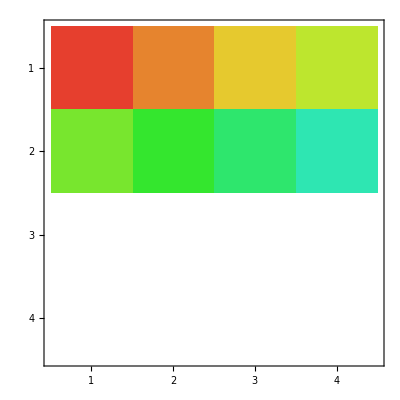

```mathematica
MatrixPlot[ArrayReshape[Range[16],{4,4}]{{1,1,1,1},{1,1,1,1},{0,0,0,0},{0,0,0,0}},ColorRules->Table[(h*n-1)/4+1->Hue[h,.8,.9],{h,1/n,1-2/n,4/n}]]
```

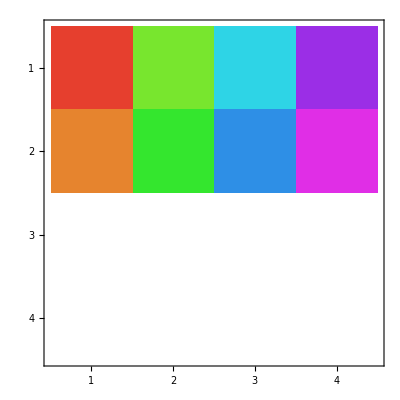

```mathematica
MatrixPlot[Transpose@ArrayReshape[Range[16],{4,4}]{{1,1,1,1},{1,1,1,1},{0,0,0,0},{0,0,0,0}},ColorRules->Table[(h*n-1)/4+1->Hue[h,.8,.9],{h,1/n,1-2/n,4/n}]]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
n=4*16;Table[(h*n-1)/4+1->Hue[h,.8,.9],{h,1/n,1-2/n,4/n}]
```

{1→Hue[Rational[1, 64], 0.8, 0.9],2→Hue[Rational[5, 64], 0.8, 0.9],3→Hue[Rational[9, 64], 0.8, 0.9],4→Hue[Rational[13, 64], 0.8, 0.9],5→Hue[Rational[17, 64], 0.8, 0.9],6→Hue[Rational[21, 64], 0.8, 0.9],7→Hue[Rational[25, 64], 0.8, 0.9],8→Hue[Rational[29, 64], 0.8, 0.9],9→Hue[Rational[33, 64], 0.8, 0.9],10→Hue[Rational[37, 64], 0.8, 0.9],11→Hue[Rational[41, 64], 0.8, 0.9],12→Hue[Rational[45, 64], 0.8, 0.9],13→Hue[Rational[49, 64], 0.8, 0.9],14→Hue[Rational[53, 64], 0.8, 0.9],15→Hue[Rational[57, 64], 0.8, 0.9],16→Hue[Rational[61, 64], 0.8, 0.9]}

```mathematica
GenericTwoQubitRho
```

{{1,α[0,1],α[0,2],α[0,3]},{α[1,0],α[1,1],α[1,2],α[1,3]},{α[2,0],α[2,1],α[2,2],α[2,3]},{α[3,0],α[3,1],α[3,2],α[3,3]}}

```mathematica
TwoQubitPCEGs[[2]]*Transpose[GenericTwoQubitRho]//MatrixForm
```

(1 | α[1,0] | 0 | 0
α[0,1] | α[1,1] | 0 | 0
α[0,2] | α[1,2] | 0 | 0
α[0,3] | α[1,3] | 0 | 0)

## 3 qubits

```mathematica
A[d_List]:=Module[{D,indicesSet},
D=Times@@d;
indicesSet=Tuples[Range[0,#-1]&/@d];
ArrayReshape[Table[Times@@Exp[2π ⅈ(-m ν+μ n)/d],{μ,#},{ν,#},{m,#},{n,#}],{D^2,D^2}]&[indicesSet]
]
```

```mathematica
PCEGenerators[d_]:=ReplaceAll[A[{d}],Table[Exp[2π ⅈ k/d]->0,{k,d-1}]]
```

```mathematica
α[0,0,0]=1;MatrixForm[GenericTwoQubitRho=ArrayReshape[Table[α[i,j,k],{i,0,3},{j,0,3},{k,0,3}],{8,8}]]
```

(1 | α[0,0,1] | α[0,0,2] | α[0,0,3] | α[0,1,0] | α[0,1,1] | α[0,1,2] | α[0,1,3]
α[0,2,0] | α[0,2,1] | α[0,2,2] | α[0,2,3] | α[0,3,0] | α[0,3,1] | α[0,3,2] | α[0,3,3]
α[1,0,0] | α[1,0,1] | α[1,0,2] | α[1,0,3] | α[1,1,0] | α[1,1,1] | α[1,1,2] | α[1,1,3]
α[1,2,0] | α[1,2,1] | α[1,2,2] | α[1,2,3] | α[1,3,0] | α[1,3,1] | α[1,3,2] | α[1,3,3]
α[2,0,0] | α[2,0,1] | α[2,0,2] | α[2,0,3] | α[2,1,0] | α[2,1,1] | α[2,1,2] | α[2,1,3]
α[2,2,0] | α[2,2,1] | α[2,2,2] | α[2,2,3] | α[2,3,0] | α[2,3,1] | α[2,3,2] | α[2,3,3]
α[3,0,0] | α[3,0,1] | α[3,0,2] | α[3,0,3] | α[3,1,0] | α[3,1,1] | α[3,1,2] | α[3,1,3]
α[3,2,0] | α[3,2,1] | α[3,2,2] | α[3,2,3] | α[3,3,0] | α[3,3,1] | α[3,3,2] | α[3,3,3])

```mathematica
TransformIndices[H_]:={2*#[[1]]+#[[3]],2*#[[2]]+#[[4]]}+1&/@H
```

```mathematica
TransformIndices[Flatten[Table[Join[{i,j},IntegerDigits[k,2,2]],{i,0,3},{j,0,3},{k,0,3}],2]]
```

{{1,1},{1,2},{2,1},{2,2},{1,3},{1,4},{2,3},{2,4},{1,5},{1,6},{2,5},{2,6},{1,7},{1,8},{2,7},{2,8},{3,1},{3,2},{4,1},{4,2},{3,3},{3,4},{4,3},{4,4},{3,5},{3,6},{4,5},{4,6},{3,7},{3,8},{4,7},{4,8},{5,1},{5,2},{6,1},{6,2},{5,3},{5,4},{6,3},{6,4},{5,5},{5,6},{6,5},{6,6},{5,7},{5,8},{6,7},{6,8},{7,1},{7,2},{8,1},{8,2},{7,3},{7,4},{8,3},{8,4},{7,5},{7,6},{8,5},{8,6},{7,7},{7,8},{8,7},{8,8}}

```mathematica
ReplaceAll[A[{2,2,2}],-1->0]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1}}

```mathematica
PCEGenerators[2]
```

{{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}}

```mathematica
KroneckerProduct[{1,1,1,1},{1,1,0,0}]
```

{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}}

```mathematica
Transpose[GenericTwoQubitRho] KroneckerProduct[{1,1,1,1},{1,1,0,0}]//MatrixForm
```

(1 | α[1,0] | 0 | 0
α[0,1] | α[1,1] | 0 | 0
α[0,2] | α[1,2] | 0 | 0
α[0,3] | α[1,3] | 0 | 0)

```mathematica
Import["/home/jadeleon/Documents/libs/Quantum2.m"]
```

i::shdw: Symbol i appears in multiple contexts {Quantum2`,Global`}; definitions in context Quantum2` may shadow or be shadowed by other definitions.

j::shdw: Symbol j appears in multiple contexts {Quantum2`,Global`}; definitions in context Quantum2` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {Quantum2`,Global`}; definitions in context Quantum2` may shadow or be shadowed by other definitions.

```mathematica
Table[PartialTrace[KroneckerProduct[Pauli[i],Pauli[j]],1],{i,0,3},{j,0,3}]
```

{{{{2,0},{0,2}},{{0,2},{2,0}},{{0,-2 ⅈ},{2 ⅈ,0}},{{2,0},{0,-2}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}}

```mathematica
S={{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

```mathematica
S//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
S//UnitaryMatrixQ
```

True

```mathematica
S.KroneckerProduct[Pauli[2],Pauli[1]].ConjugateTranspose[S]==KroneckerProduct[Pauli[1],Pauli[2]]
```

True

```mathematica
ConjugateTranspose[S].KroneckerProduct[Pauli[2],Pauli[1]].S==KroneckerProduct[Pauli[1],Pauli[2]]
```

True